```mathematica
v=9;
Logmaxdgdd[v]
Logvvpmaxdgdd[v]
pmaxdgdd[v]
```

```mathematica
Logmaxdgdd[v]={{Log[5000],3.0811151263243617},{Log[10000],2.9015238553373988},{Log[20000],2.7106688527724607},{Log[30000],2.610442884899177},{Log[50000],2.523909941470408}};
```

```mathematica
Logvvpmaxdgdd[v]={{Log[5000],-3.592897068472406},{Log[10000],-3.8752634916196365},{Log[20000],-3.930004202535882},{Log[30000],-3.9727304744263137},{Log[50000],-4.196067701162642}};
```

```mathematica
pmaxdgdd[v]={{5000,0.0853},{10000,0.08410000000000001},{20000,0.0835},{30000,0.0833},{50000,0.0829}};
```

```mathematica
ν=1/0.13;
k0=0.08122;
ClearAll[a0,b0,d0,ex0,c0]
model1=a0*x-b0;
model2=d0+c0*x^(-ex0)
model3=d0+c0*x^(-1/ν)
model4=k0+c0*x^(-ex0)

nlf1=NonlinearModelFit[Logvvpmaxdgdd[v],model1,{a0,b0},x];

nlf1[{"BestFit","ParameterTable"}]


nlf2=NonlinearModelFit[pmaxdgdd[v],model2,{d0,c0,ex0},x];

nlf2[{"BestFit","ParameterTable"}]


nlf3=NonlinearModelFit[pmaxdgdd[v],model3,{d0,c0},x];

nlf3[{"BestFit","ParameterTable"}]


nlf4=NonlinearModelFit[pmaxdgdd[v],model4,{ex0,c0},x];

nlf4[{"BestFit","ParameterTable"}]
```

d0+c0 x^-ex0

d0+c0/x^0.13

0.08122+c0 x^-ex0

{-1.68001-0.229019 x, | Estimate | Standard Error | t-Statistic | P-Value
a0 | -0.229019 | 0.0392838 | -5.82986 | 0.0100533
b0 | 1.68001 | 0.384418 | 4.37027 | 0.0221612}

{0.08382-442.003/x^58.4948, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.08382 | 0.000590593 | 141.925 | 0.0000496419
c0 | -442.003 | 0. | -∞ | 0.
ex0 | 58.4948 | 0. | ∞ | 0.}

{0.0761314+0.0271638/x^0.13, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.0761314 | 0.000858723 | 88.6565 | 3.1633×10^-6
c0 | 0.0271638 | 0.00301676 | 9.0043 | 0.00289178}

{0.08122+0.10913/x^0.388496, | Estimate | Standard Error | t-Statistic | P-Value
ex0 | 0.388496 | 0.0274275 | 14.1645 | 0.000762307
c0 | 0.10913 | 0.0277715 | 3.92957 | 0.0293385}

```mathematica
a
```

-0.226382

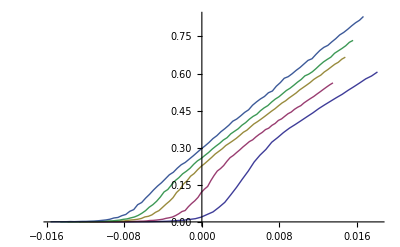

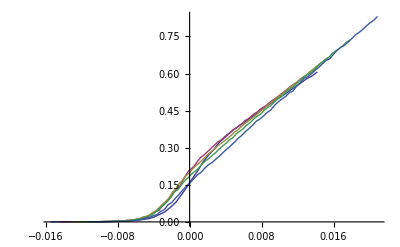

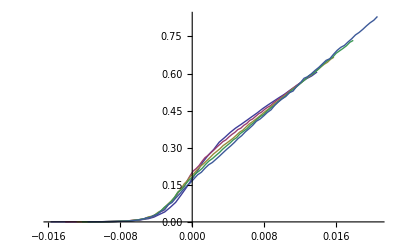

0.08122 =d0

0.13 =z

0.226382+=a

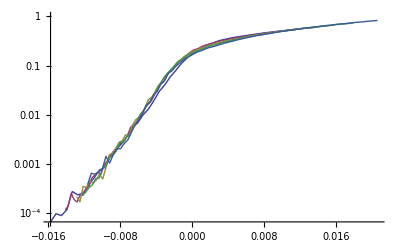

```mathematica
b0=0.13;
k01=nlf2["ParameterTableEntries"][[1]][[1]];
k02=nlf3["ParameterTableEntries"][[1]][[1]];
k03=k0;
ex01=-nlf2["ParameterTableEntries"][[3]][[1]];
ex02=-1/ν;
ex03=-nlf4["ParameterTableEntries"][[1]][[1]];
a=-nlf1["ParameterTableEntries"][[2]][[1]];
c01=nlf2["ParameterTableEntries"][[2]][[1]];
c02=nlf3["ParameterTableEntries"][[2]][[1]];
c03=nlf4["ParameterTableEntries"][[2]][[1]];


Do[

(*absMs1[l]=Table[{(absM[l][[All,1]][[i]]),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

absMs2[l]=Table[{(absM[l][[All,1]][[i]]-(k0+c0*l^(ex0))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

absMs[l]=Table[{(absM[l][[All,1]][[i]]-(k0+c0*l^(ex0)))*l^b,absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];*)

gaps1[v][l]=Table[{(gap[v][l][[All,1]][[i]]-(k01+c01*(l*1000)^(ex01)))*(l*1000)^b0,gap[v][l][[All,2]][[i]]*(l*1000)^(-a)},{i,1,Length[gap[v][l]]}];

gaps2[v][l]=Table[{(gap[v][l][[All,1]][[i]]-(k02+c02*(l*1000)^(ex02)))*(l*1000)^b0,gap[v][l][[All,2]][[i]]*(l*1000)^(-a)},{i,1,Length[gap[v][l]]}];

gaps3[v][l]=Table[{(gap[v][l][[All,1]][[i]]-(k03+c03*(l*1000)^(ex03)))*(l*1000)^b0,gap[v][l][[All,2]][[i]]*(l*1000)^(-a)},{i,1,Length[gap[v][l]]}];

,{l,{5,10,20,30,50}}]
(*ListLogPlot[{absM[16],absM[24],absM[32],absM[48],absM[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs1[16],absMs1[24],absMs1[32],absMs1[48],absMs1[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs2[16],absMs2[24],absMs2[32],absMs2[48],absMs2[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs[16],absMs[24],absMs[32],absMs[48],absMs[64]},Joined->True,PlotMarkers->Automatic]*)
ListPlot[{gaps1[v][5],gaps1[v][10],gaps1[v][20],gaps1[v][30],gaps1[v][50]},Joined->True]
ListPlot[{gaps2[v][5],gaps2[v][10],gaps2[v][20],gaps2[v][30],gaps2[v][50]},Joined->True]
ListPlot[{gaps3[v][5],gaps3[v][10],gaps3[v][20],gaps3[v][30],gaps3[v][50]},Joined->True]
"=d0 "k03
"=z " b0
"=a " -a
ListLogPlot[{gaps3[v][5],gaps3[v][10],gaps3[v][20],gaps3[v][30],gaps3[v][50]},Joined->True]
```

```mathematica
l1=20;
l2=50;

Do[
(*input1[l]=Table[{(absM[l][[All,1]][[i]]-(k01+c01*l^(ex01))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

input2[l]=Table[{(absM[l][[All,1]][[i]]-(k02+c02*l^(ex02))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];*)

input3[l]=Table[{(gap[v][l][[All,1]][[i]]-(k03+c03*(l*1000)^(ex03))),gap[v][l][[All,2]][[i]]*l^(-a)},{i,1,Length[gap[v][l]]}];
,{l,{l1,l2}}]

aux=1000;
For[z=-0.2,z<0.4,z+=0.01,
ClearAll[i];

Do[
dat[l]=Table[{input3[l][[All,1]][[i]]*(l*1000)^z,input3[l][[All,2]][[i]]},{i,1,Length[input3[l]]}];
i[l]=Interpolation[dat[l]]
,{l,{l1,l2}}];


min=Max[dat[l1][[All,1]][[1]],dat[l2][[All,1]][[1]]];
max=Min[dat[l1][[All,1]][[Length[dat[l1]]]],dat[l2][[All,1]][[Length[dat[l2]]]]];

val=NIntegrate[Abs[i[l1][x]-i[l2][x]],{x,min,max}]/(max-min);
(*Print[val]*)

If[val<aux,
aux=val;
zf=z;
]
]

aux
"= zf"zf
```

0.00210405

0.13 = zf

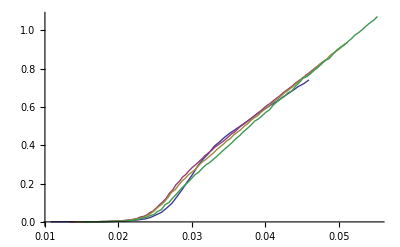
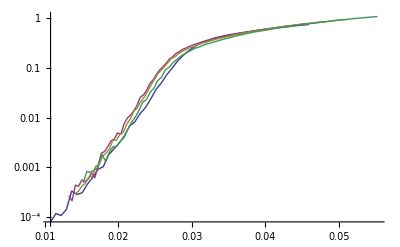
```mathematica
(*Old Method:*)
ClearAll[d0,a,z]
ClearAll[i];
ClearAll[d0,a,z]
l1=50;
l2=20;
l3=30;
l4=50;
sum={};

Do[

input3[l]=Table[{(gap[v][l][[All,1]][[i]]),gap[v][l][[All,2]][[i]]},{i,1,Length[gap[v][l]]}]
,{l,{l1,l2,l3,l4}}]




*(Max[in[l1][max],in[l2][max],in[l3][max],in[l4][max]]-Min[in[l1][min],in[l2][min],in[l3][min],in[l4][min]])

aux=1000;
For[d0=0.076,d0<0.086,d0+=0.001,
For[a=-0.3,a<0.35,a+=0.05,
For[z=-0.3,z<0.3,z+=0.05,


Do[
dat[l]=Table[{(input3[l][[All,1]][[i]]-d0)*(l*1000)^z,input3[l][[All,2]][[i]]}*(l*1000)^a,{i,1,Length[input3[l]]}];
in[l]=Interpolation[dat[l]]
,{l,{l1,l2,l3,l4}}];


min=Max[dat[l1][[All,1]][[1]],dat[l2][[All,1]][[1]],dat[l3][[All,1]][[1]],dat[l4][[All,1]][[1]]];
max=Min[dat[l1][[All,1]][[Length[dat[l1]]]],dat[l2][[All,1]][[Length[dat[l2]]]],dat[l3][[All,1]][[Length[dat[l3]]]],dat[l4][[All,1]][[Length[dat[l4]]]]];

val=NIntegrate[Abs[Log[Max[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]-Log[Min[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]],{x,min,max}]/((max-min)*(Log[Max[in[l1][max],in[l2][max],in[l3][max],in[l4][max]]]-Log[Min[in[l1][min],in[l2][min],in[l3][min],in[l4][min]]]));
(*Print[val]*)
(*sum=Append[sum,{z,val}];*)

If[val<aux,
aux=val;
zf=z;
af=a;
d0f=d0;
]
]
]
]
aux
"= zf"zf
"= af" af
"= d0f" d0f
0.03867024437161889
-0.10000000000000002 "= zf"
0.25 "= af"
0.077 "= d0f"
af=0.22638171579816446;
d0f=0.077
0.077
zf=-0.1;
af=0.25;
d0f=0.077;

(*zf=0.09;
af=0.09;
d0f=0.079;*)


l1=5;
l2=20;
l3=30;
l4=50;

Do[

input3[l]=Table[{(gap[v][l][[All,1]][[i]]),gap[v][l][[All,2]][[i]]},{i,1,Length[gap[v][l]]}];
dat[l]=Table[{(input3[l][[All,1]][[i]]-d0f)*(l*1000)^zf,input3[l][[All,2]][[i]]}*(l*1000)^af,{i,1,Length[input3[l]]}];
i[l]=Interpolation[dat[l]]
,{l,{l1,l2,l3,l4}}];
ListLinePlot[{dat[l1],dat[l2],dat[l3],dat[l4]}]
ListLogPlot[{dat[l1],dat[l2],dat[l3],dat[l4]},Joined->True,PlotRange->Full]

-Graphics-
-Graphics-
l1
10
gap[9][10]
```

```mathematica
-------------------------------------------------
```

0.000203965

0.05 = zf

-0.3 = af

0.083 = d0f

```mathematica
10000000000000^(0.1)
```

19.9526

```mathematica
ClearAll[d]
l=1000000
z1=-0.1
z=0.13
c=-0.39
d0=0.08122;
δ=-0.4;
(d*l^z1-(d0+δ)*l^z1)-(d*l^z-(d0+b*l^c)*l^z)
```

1000000

-0.1

0.13

-0.39

0.613682-5.77441 d

```mathematica
ClearAll[dif]
```

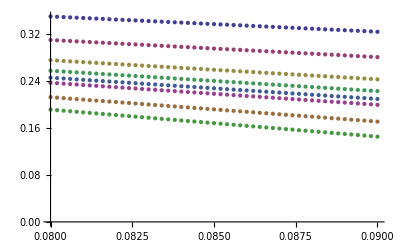

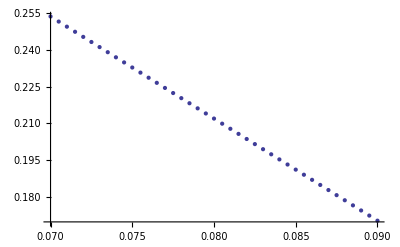

```mathematica
Do[
dif[l]=Table[{d,(d*(l*1000)^z1-(d0+δ)*(l*1000)^z1)-(d*(l*1000)^z-(d0+b*(l*1000)^c)*(l*1000)^z)},{d,0.08,0.09,0.0002}];
,{l,{5,10,20,30,40,50,100,200}}]
ListPlot[{dif[5],dif[10],dif[20],dif[30],dif[40],dif[50],dif[100],dif[200]}]
```